Get::noopen: Cannot open Graphics`Legend`.

Needs::nocont: Context Graphics`Legend` was not created when Needs was evaluated.

$Failed

ⅇ^(ⅈ kL x)+ⅇ^(-ⅈ kL x) R

kL→√2 √((En m)/ℏ^2)

ⅇ^(ⅈ kR x) T

kR→√2 √((m (En-V0))/ℏ^2)

{1+R==T,ⅈ kL-ⅈ kL R==ⅈ kR T}

{R→(kL-kR)/(kL+kR),T→(2 kL)/(kL+kR)}

{-(kL (-1+R^2) ℏ)/m,0,0}

{(kL ℏ)/m,0,0}

{(kL R^2 ℏ)/m,0,0}

{(kR T^2 ℏ)/m,0,0}

(kL-kR)^2/(kL+kR)^2

(4 kL kR)/(kL+kR)^2

1

{m→1,ℏ→1,V0→1}

Plot::optx: Unknown option PlotLegend→{RR,TT,TT+RR} in Plot[{(-√2 √Plus[«2»]+√2 √En)^2/(√2 √Plus[«2»]+√2 √En)^2,(8 √(-1+En) √En)/(√2 √Plus[«2»]+√2 √En)^2,(-Power[«2»] Power[«2»]+Power[«2»] Power[«2»])^2/(Power[«2»] Power[«2»]+Power[«2»] Power[«2»])^2+(8 √(-1+En) √En)/(Power[«2»] Power[«2»]+«1» «1»)^2},{En,1,2},AxesLabel→{E,Coeficientes},«1»,«1»,LegendPosition→{1,-1/2},PlotRange→{0,1}].

Plot[{(-√2 √(-1+En)+√2 √En)^2/(√2 √(-1+En)+√2 √En)^2,(8 √(-1+En) √En)/(√2 √(-1+En)+√2 √En)^2,(-√2 √(-1+En)+√2 √En)^2/(√2 √(-1+En)+√2 √En)^2+(8 √(-1+En) √En)/(√2 √(-1+En)+√2 √En)^2},{En,1,2},AxesLabel→{E,Coeficientes},PlotStyle→{Dashing[{0.06,0.02}],Dashing[{0.02}],{}},PlotLegend→{RR,TT,TT+RR},LegendPosition→{1,-1/2},PlotRange→{0,1}]

{kL→√2 √((En m)/ℏ^2),kR→√2 √((m (En-V0))/ℏ^2)}

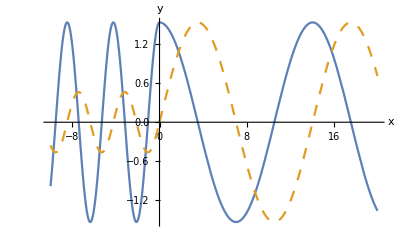

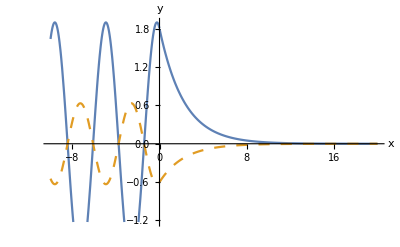

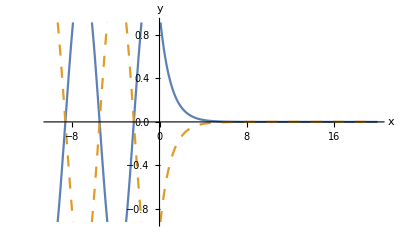

{En→V+(kW^2 ℏ^2)/(2 m)}

(C[1]+C[2]) Cos[kW x]+ⅈ (C[1]-C[2]) Sin[kW x]

kW→(√2 √(m (V0-Wn)))/ℏ

cSym Cos[kW x]+cAsym Sin[kW x]

{En→(kLR^2 ℏ^2)/(2 m)}

ⅇ^(ⅈ kLR x) C[1]+ⅇ^(-ⅈ kLR x) C[2]

kLR→(ⅈ √2 √m √Wn)/ℏ

qLR→(√2 √(m Wn))/ℏ

ⅇ^(qRL x) C[1]+ⅇ^(-qRL x) C[2]

{cL ⅇ^(-a qLR)-cSym Cos[a kW]+cAsym Sin[a kW]==0,-cR ⅇ^(-a qLR)+cSym Cos[a kW]+cAsym Sin[a kW]==0,cL ⅇ^(-a qLR) qLR-cAsym kW Cos[a kW]-cSym kW Sin[a kW]==0,cR ⅇ^(-a qLR) qLR+cAsym kW Cos[a kW]-cSym kW Sin[a kW]==0}

cL ⅇ^(-a qLR)-cSym Cos[a kW]==0
-cR ⅇ^(-a qLR)+cSym Cos[a kW]==0
cL ⅇ^(-a qLR) qLR-cSym kW Sin[a kW]==0
cR ⅇ^(-a qLR) qLR-cSym kW Sin[a kW]==0

Cos[a kW]≠0
cSym kW Sin[a kW]≠0
qLR==kW Tan[a kW]
cL==cSym ⅇ^(a qLR) Cos[a kW]
cR==cSym ⅇ^(a qLR) Cos[a kW]

{}

Tan[a kW]==qLR/kW

cAsym kW Cos[a kW] Sin[a kW]≠0
qLR==-kW Cot[a kW]
cL==-cAsym ⅇ^(-a kW Cot[a kW]) Sin[a kW]
cR==cAsym ⅇ^(a qLR) Sin[a kW]

{}

Tan[a kW]==-kW/qLR

{a→1,m→1,ℏ→1,V0→{100,200,500,∞}}

Wn→V0-(n^2 π^2 ℏ^2)/(8 a^2 m)

{kW→(√2 √(m (V0-Wn)))/ℏ,qLR→(√2 √(m Wn))/ℏ}

Tan[(n π)/2]==(2 √2 a √m √(V0-(n^2 π^2 ℏ^2)/(8 a^2 m)))/(n π ℏ)

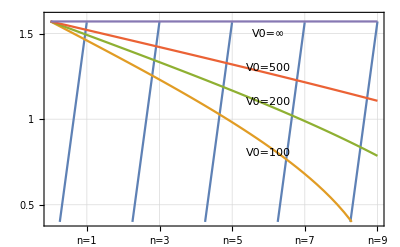

Tan[(n π)/2]==-(n π ℏ)/(2 √2 a √m √(V0-(n^2 π^2 ℏ^2)/(8 a^2 m)))

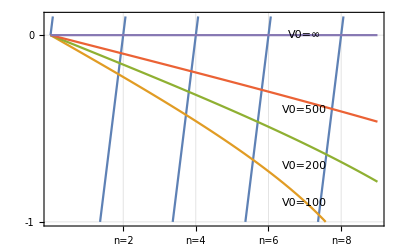

```mathematica
(*Potencial escalón finito*)
Needs["Graphics`Legend`"]
Clear["Global`*"]
ψL [x_]=ⅇ^(ⅈ kL x)+ ⅇ^(-ⅈ kL x) R
kLRule=kL->√2 √((En m)/ℏ^2)
ψR[x_]= ⅇ^(ⅈ kR x)  T
kRRule=kR->√2 √(((En-V0) m)/ℏ^2)
boundary={ψL[x]==ψR[x],ψL'[x]==ψR'[x]}/. x->0
RTrule = Solve[boundary,{R,T}]//Flatten//Simplify
SuperStar[exp_]:=exp/. {Complex[a_,b_]:>Complex[a,-b]}
∇f_:=D[f,#]&/@{x,y,z}
flux[ψ_]:=ℏ/(2ⅈ m)(SuperStar[ψ] ∇ψ-∇SuperStar[ψ] ψ)//Simplify
ψL[x]//flux//Simplify
incFlux=flux[ψL[x]]/. {R->0}
Rflux=(incFlux-flux[ψL[x]])//Simplify
Tflux=flux[ψR[x]]
RR=Rflux[[1]]/incFlux[[1]]/. RTrule
TT=Tflux[[1]]/incFlux[[1]]/. RTrule
RR+TT//Simplify
values={m->1,ℏ->1,V0->1}
Plot[{RR,TT,TT+RR}/.RTrule/.kLRule/.kRRule/.values//Evaluate,{En,1,2},AxesLabel->{"E","Coeficientes"},PlotStyle->{Dashing[{0.06,0.02}],Dashing[{0.02}],{}},PlotLegend->{"RR","TT","TT+RR"},LegendPosition->{1,-1/2},PlotRange->{0,1}]
kRule={kLRule,kRRule}
wave[x_,En_]={ψL[x],ψR[x]}/.RTrule/.kRule/.values//Simplify;
ψ[x_,En_]:=Which[x≤0,wave[x,En][[1]],x>0,wave[x,En][[2]]]
waveplot2D[Energy_]:=Plot[{ψ[x,Energy]//Re,ψ[x,Energy]//Im},{x,-10,20},PlotStyle->{{},Dashing[{0.02}]},AxesLabel->{"x","y"}]
waveplot2D[1.1]
waveplot2D[0.9]
waveplot2D[0.5]
(*Potencial pozo finito*)
Clear["Global`*"]
schrodeq=0==(V-En)ψ[x]-(ℏ^2 ψ''[x])/(2m);
EWrule={En->(kW^2 ℏ^2)/(2m)+V}
ψ[x]/. DSolve[schrodeq,ψ[x],x][[1]]/. EWrule //ExpToTrig//Simplify//PowerExpand
kWrule=kW->(√2 √(m(En-V)))/ℏ/. V->-V0/. En->-Wn
ψW[x_]=cSym Cos[kW x]+cAsym Sin[kW x]
ELRrule ={En->(kLR^2 ℏ^2)/(2 m)}
ψ[x]/. DSolve[schrodeq,ψ[x],x][[1]]/. V->0/. ELRrule //Simplify//PowerExpand
kLRrule=kLR->(√2 √(En m))/ℏ/. En->-Wn//PowerExpand
qLRrule=qLR->(√2 √(Wn m))/ℏ
ψ[x]/. DSolve[schrodeq,ψ[x],x][[1]]/. V->0/. ELRrule /. kLR->I qRL//Simplify//PowerExpand
ψR[x_]=cR ⅇ^(-qLR x) ; (*x > a*)
ψL[x_]=cL ⅇ^(+qLR x) ; (*x < -a*)
eq1={(ψL[x]-ψW[x]==0)/. {x->-a},(ψW[x]-ψR[x]==0)/. {x->+a}, (ψL '[x]-ψW '[x]==0)/. {x->-a},(ψW '[x]-ψR '[x]==0)/. {x->+a}}
(eq2=eq1/. cAsym->0)//ColumnForm
eq3=Reduce[{eq2,cL≠0,cR≠0,kW≠0,qLR≠0,cSym≠0,Cos[a kW]≠0}//Flatten,{cL,cR}]; eq3// ColumnForm
symSol=Solve[eq3,{cL,cR}]//Simplify//Flatten
symEn=Tan[a kW]==qLR /kW
eq4=Reduce[{eq1/. cSym->0,cL≠0,cR≠0,kW≠0,qLR≠0,cAsym≠0,Cos[a kW]≠0}//Flatten,{cL,cR}]; eq4// ColumnForm
asymSol=Solve[eq4,{cL,cR}]//Simplify//Flatten
asymEn=Tan[a kW]==-kW/qLR
values={a->1,m->1,ℏ->1,V0->{100,200,500,∞}}
nRule=Wn->V0-(n^2 π^2 ℏ^2)/(8 a^2 m)
kRules={kW->(√2 √(m (V0-Wn)))/ℏ,qLR->(√2 √(m (Wn)))/ℏ}
eq5=symEn/. kRules/. nRule//PowerExpand
pt1=Plot[{ArcTan[eq5[[1]]],ArcTan[eq5[[2]]]}/. values//Evaluate,{n,0,9},Frame->True,FrameTicks->{{{1,"n=1"},{3,"n=3"},{5,"n=5"},{7,"n=7"},{9,"n=9"}},{0,0.5,1,1.5}},PlotRange->{0.4,1.6},DisplayFunction->Identity];
text={Text["V0=∞",{6,1.5}],Text["V0=500",{6,1.3}],Text["V0=200",{6,1.1}],Text["V0=100",{6,0.8}]};
Show[pt1,Graphics[text],GridLines->Automatic,DisplayFunction->$DisplayFunction]
eq6=asymEn/. kRules/. nRule//PowerExpand
text={Text["V0=∞",{7,0}],Text["V0=500",{7,-0.4}],Text["V0=200",{7,-0.7}],Text["V0=100",{7,-0.9}]};
Plot[{ArcTan[eq6[[1]]],ArcTan[eq6[[2]]]}/. values//Evaluate,{n,0,9},Frame->True,FrameTicks->{{{2,"n=2"},{4,"n=4"},{6,"n=6"},{8,"n=8"}},{-1.5,-1,0,0.5,1,1.5}},PlotRange->{-1,0.1},GridLines->Automatic,Epilog->text]
```